## Interraction of two bar magnets

```mathematica
Fmagn[x_]:= (B0^2 A^2(L^2+R^2))/(π μ0 L^2)(1/x^2+1/(x+2L)^2-2/(x+L)^2)
```

```mathematica
μ0 = 1.26*10^-6;
B0 = 10^-5;
R = 0.01;
A = π R^2;
L = 0.1;
```

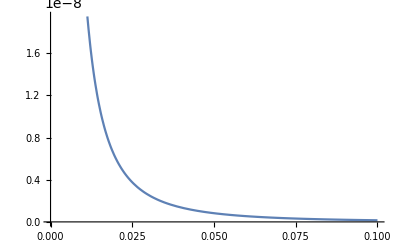

```mathematica
Plot[Fmagn[x],{x, 0, 0.1}]
```

## Force of a leaf spring

q1 = 4 for rectangular spring

```mathematica
Fspring[s_]:=(b Em h^3 s)/(Ls^3 4)
```

```mathematica
Ls = 1;
h = 1*10^-3;
b=2*10^2;
Em = 2*10^11;
```